```mathematica
parse[s_]:=ToExpression@StringReplace[s,{" "->"", "("->"{",")"->"}","Vector("->"{","E"->"*10^"}]
```

```mathematica
model=a x^n+c;
```

```mathematica
(*model=a n^x+c;*)
```

```mathematica
fitDegree[data_]:=FindFit[data,model,{a,n,c},x]
```

```mathematica
plotTogehter[data_, rule_]:=With[{expr=model/.rule},
Show[
Plot[expr,{x,data[[1,1]],data[[-1,1]]}],
ListPlot[data,PlotStyle->Red],PlotLabel->expr]]
```

```mathematica
fitAndPlot[data_]:=plotTogehter[data,fitDegree[data]]
```

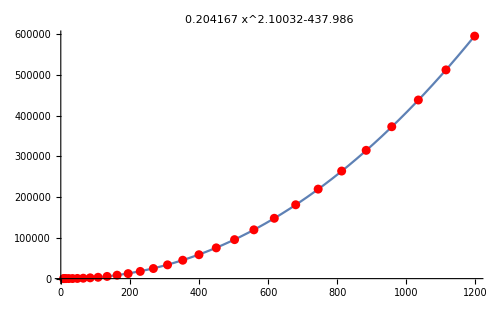

```mathematica
s=ReadString[NotebookDirectory[]<> "FitterData.txt"];
fitAndPlot[parse[s]]
```

```mathematica
s
```

Vector((8.0,41.0), (10.0,50.0), (15.0,73.0), (23.0,133.0), (34.0,206.0), (48.0,444.0), (65.0,997.0), (85.0,1924.0), (108.0,3281.0), (134.0,5414.0), (163.0,8445.0), (195.0,12292.0), (230.0,17695.0), (268.0,24783.0), (309.0,33815.0), (353.0,45160.0), (400.0,58687.0), (450.0,75510.0), (503.0,95735.0), (559.0,119798.0), (618.0,148168.0), (680.0,181365.0), (745.0,219820.0), (813.0,264172.0), (884.0,315073.0), (958.0,373036.0), (1035.0,438665.0), (1115.0,512618.0), (1198.0,595574.0))